## Parameters

```mathematica
sw=0.2;
s1=0.6;
Zr=300;
α=25/1000;
λ=0.33/10;
kQ=0.001;
n=0.35;
kc=0.1(*1/10*);
Aleak=1.;
Naleak=1;
X2leak=0.01;
Keq=10^-3; (*10^-3, White et al, 2008*)
(*Keq=10^-4.02;*)
Ksol=6*10^-9;
Kw=10^-14;
Ka1=10^-6.3;
Ka2=10^-10.3;
He=0.83;
R=0.0821/10^3;
Tatm=298;
(*L=α λ;*)
patm[L_]:=10^-3.5+L kc;
wmax=2.7 10^-6;(*10^-17*60*60*24*1.6*10^6*1.94-rate from White&Brantely, 2003, density and specific area from White et al, 2008*)
(*wmax=1*10^-6;*)
ρsa=96.11;(*96.11 g/mol silicic acid*)
```

## Expressions

### General

```mathematica
α0[H_]:=(1+Ka1/H+Ka1 Ka2/H^2)^-1;
α1[H_]:=(H/Ka1+1+Ka2/H)^-1;
α2[H_]:=(H^2/(Ka1 Ka2)+H/Ka2+1)^-1;
Ct[H_,L_]:=(He patm[L] 10^0)/(α0[H]R Tatm);
H[A_,ct_]:=Last[H/.Quiet[Solve[A==ct(α1[H]+2 α2[H])+Kw/H-H,{H}]]]
Wr[A_,ct_,Na_,X2_]:=wmax(1-α1[H[A,ct]]/(α0[H[A,ct]] Keq)Na X2^2)
r[A_,H_,ct_]:=A-ct(α1[H]+2 α2[H])+Kw/H-H
```

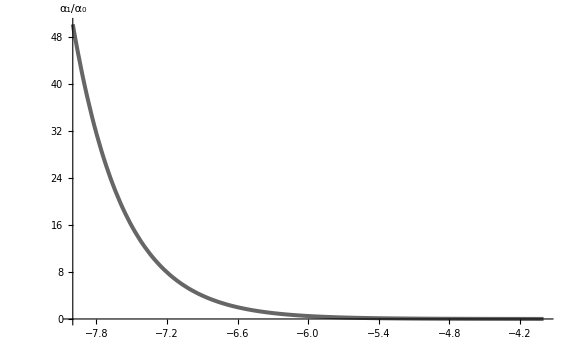
-Graphics-pH

```mathematica
Labeled[Plot[α1[10^-p]/α0[10^-p],{p,4,8},PlotRange->All,ScalingFunctions->{"Reverse",Identity},PlotStyle->{GrayLevel[0.4],Thickness[0.005]},AxesStyle->Directive[Black, 20],AxesLabel->{None,Framed[Style["α_1/α_0",Italic],FrameStyle->None, BaseStyle->{24}]},ImageSize->Large],Style["pH",Italic],LabelStyle->Directive[Black, 20,Italic]]
```

### Leakage composition

```mathematica
sol[L_,Aleak_]:=Solve[Aleak==Ct[x,L](α1[x]+2 α2[x])+Kw/x-x,x];
Hleak[L_,Aleak_]:=x/.Last[Quiet[Solve[Aleak==Ct[x,L](α1[x]+2 α2[x])+Kw/x-x,x]]];
Ctleak[L_,Aleak_]:=Ct[Hleak[L,Aleak],L];
```

```mathematica
(*ctlAk05=Table[Ctleak[l,0.5],{l,0.000001,0.01,0.000001}];*)
ctlAk1=Table[Ctleak[l,1],{l,0.000001,0.01,0.000001}];
(*ctlAk15=Table[Ctleak[l,1.5],{l,0.000001,0.01,0.000001}];
ctlAk2=Table[Ctleak[l,2],{l,0.000001,0.01,0.000001}];*)
```

```mathematica
pHleak=Table[-Log10[Hleak[L,Aleak]],{L,0.000001,.02,0.00001},{Aleak,{0.5,1,1.5,2}}];
```

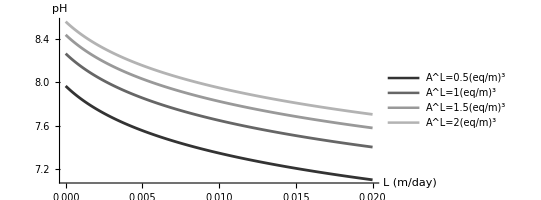

```mathematica
ListLinePlot[Transpose[pHleak],DataRange->{0.000001,.02},ImageSize->Full,LabelStyle->Directive[Black,30],PlotStyle->{Directive[GrayLevel[.2],Thickness[.005]],Directive[GrayLevel[.4],Thickness[.005]],Directive[GrayLevel[.6],Thickness[.005]],Directive[GrayLevel[.7],Thickness[.005]]},PlotLegends->Placed[{Row[{"A^L=0.5", , Style["eq/m",Plain]^3}],Row[{"A^L=1", , Style["eq/m",Plain]^3}],Row[{"A^L=1.5", , Style["eq/m",Plain]^3}],Row[{"A^L=2", , Style["eq/m",Plain]^3}]},{.9,.8}],AxesLabel->{Framed[Style["L",Italic]"(m/day)",FrameStyle->None,FrameMargins->5],Style["pH",Italic]},AxesStyle->Directive[30],AspectRatio->1/2]
```

```mathematica
Last[Style[{"A^L=0.5"},Italic][[1]] Style[{"eq/m^3"},Plain][[1]]]
```

eq/m^3 A^L=0.5

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Figure21.pdf"]]]
```

```mathematica
Export["pHLeak.dat",pHleak]
```

pHLeak.dat

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["pHLeak.dat"]]]
```

```mathematica
Export["ctlAk05.dat",ctlAk05];
Export["ctlAk1.dat",ctlAk1];
Export["ctlAk15.dat",ctlAk15];
Export["ctlAk2.dat",ctlAk2];
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["ctlAk05.dat"]]]
```

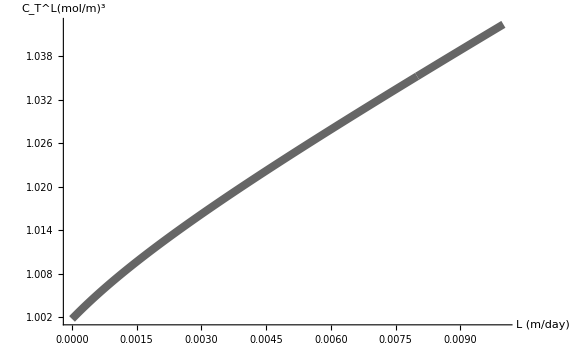

```mathematica
ListLinePlot[ctlAk1,DataRange->{0.000001,0.01},AxesLabel->{Framed[Style["L",Italic]"(m/day)",FrameStyle-> None,FrameMargins-> 10],Row[{Style["C_T^L",{Italic}],Style["mol/m",Plain]^3}]},ImageSize->Large,LabelStyle->Directive[Black,20],PlotStyle->{Directive[GrayLevel[0.4],Thickness[.01]]},ImageMargins->{{5,5},{5,5}},AxesStyle->Thickness[0.0023]]
```

```mathematica
Export["Figure22.pdf",ListLinePlot[ctlAk1,DataRange->{0.000001,0.01},AxesLabel->{"L (m/day)","C_T^L(mol/m^3)"},ImageSize->Large,LabelStyle->Directive[Black,15],PlotStyle->{Directive[GrayLevel[0.4],Thickness[.01]]},ImageMargins->{{5,5},{5,5}}]]
```

Figure22.pdf

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Figure22.pdf"]]]
```

## Steady State Calculations

### Weathering zone (Linear case)

```mathematica
h[L_]:=L/kQ;
sol1[L_,Aleak_,wmax_,Naleak_,X2leak_,kQ_]:=FindRoot[{A==Aleak+wmax/kQ(1-α1[x]/(α0[x] Keq)Na X2^2),A==Ctleak[L,Aleak](α1[x]+2 α2[x])+Kw/x-x,Na==Naleak+wmax/kQ(1-α1[x]/(α0[x] Keq)Na X2^2),X2==X2leak+(2 wmax)/kQ(1-α1[x]/(α0[x] Keq)Na X2^2)},{{A,Aleak},{x,Hleak[L,Aleak]},{Na,Naleak},{X2,X2leak}}];
A[L_,Aleak_,wmax_,Naleak_,X2leak_,kQ_]:=A/.sol1[L,Aleak,wmax,Naleak,X2leak,kQ];
pH[L_,Aleak_,wmax_,Naleak_,X2leak_,kQ_]:=-Log10[x]/.sol1[L,Aleak,wmax,Naleak,X2leak,kQ];
Na[L_,Aleak_,wmax_,Naleak_,X2leak_,kQ_]:=Na/.sol1[L,Aleak,wmax,Naleak,X2leak,kQ];
X2[L_,Aleak_,wmax_,Naleak_,X2leak_,kQ_]:=X2/.sol1[L,Aleak,wmax,Naleak,X2leak,kQ];
W[L_,Aleak_,wmax_,Naleak_,X2leak_,kQ_]:= wmax(1-α1[x]/(α0[x] Keq)Na[L,Aleak,wmax,Naleak,X2leak,kQ] X2[L,Aleak,wmax,Naleak,X2leak,kQ]^2)/.sol1[L,Aleak,wmax,Naleak,X2leak,kQ]
```

```mathematica
FindRoot[X2[L,.2 Aleak,wmax,1,0.01,kQ]==0.01,{L,0.01}]//Quiet
```

{L→0.00272132}

```mathematica
Na[0.2,Aleak,wmax,1,0.01,kQ]
```

1.0027

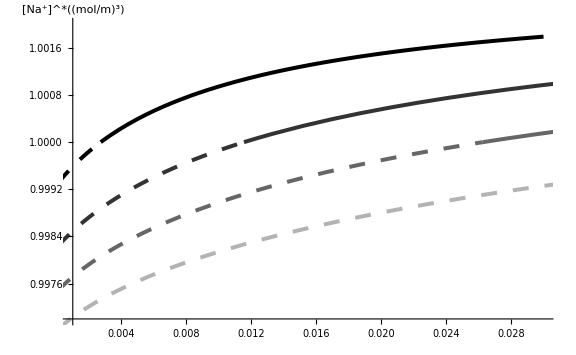
-Graphics-L(m/day)

```mathematica
Labeled[Show[Plot[{Na[L,.2Aleak,wmax,1,0.01,kQ]},{L,0.0027213242259699565,0.03},PlotRange->{{0.001,0.03},{0.997,1.002}},PlotStyle->{Black,Thickness[0.005]},AxesStyle->Directive[Black, 20],AxesLabel->{None,Framed[Row[{Style["[Na^+]^*",Italic],("(mol/m")^3,")"}],FrameStyle->None,FrameMargins->10]},Ticks->{Automatic,Automatic},TicksStyle->{Directive[FontOpacity->0,FontSize->0],Automatic}],Plot[{Na[L,.2Aleak,wmax,1,0.01,kQ]},{L,0.0001,0.0027213242259699565},PlotStyle->{Black,Thickness[0.005],Dashing[0.02]}],Plot[{Na[L,Aleak,wmax,1,0.01,kQ]},{L,0.02625574935162154,0.1},PlotRange->{{0.001,0.03},{0.997,1.002}},PlotStyle->{GrayLevel[0.4],Thickness[0.005]},AxesStyle->Directive[Black, 20],AxesLabel->{None,Framed[Row[{Style["[Na^+]^*",Italic],("(mol/m)")^3}],FrameStyle->None,FrameMargins->10]},Ticks->{Automatic,Automatic},TicksStyle->{Directive[FontOpacity->0,FontSize->0],Automatic}],Plot[{Na[L,Aleak,wmax,1,0.01,kQ]},{L,0.0001,0.02625574935162154},PlotStyle->{GrayLevel[0.4],Thickness[0.005],Dashing[0.02]}],Plot[{Na[L,0.5Aleak,wmax,1,0.01,kQ]},{L,0.011546733648089638,0.1},PlotStyle->{GrayLevel[0.2],Thickness[0.005]},AxesStyle->Directive[Black, 20]],Plot[{Na[L,0.5Aleak,wmax,1,0.01,kQ]},{L,0.0001,0.011546733648089638},PlotStyle->{GrayLevel[0.2],Thickness[0.005],Dashing[0.02]}],
Plot[{Na[L,2Aleak,wmax,1,0.01,kQ]},{L,0.05567378075868801,0.1},PlotStyle->{GrayLevel[0.7],Thickness[0.005]},AxesStyle->Directive[Black, 20]],Plot[{Na[L,2Aleak,wmax,1,0.01,kQ]},{L,0.0001,0.05567378075868801},PlotStyle->{GrayLevel[0.7],Thickness[0.005],Dashing[0.02]}],ImageSize-> Large],Row[{Style["L",Italic],"(m/day)"}],LabelStyle->Directive[Black, 20]]
```

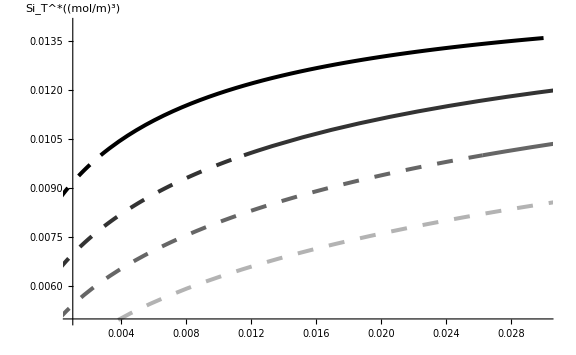
-Graphics-L(m/day)

```mathematica
Labeled[Show[Plot[{X2[L,.2Aleak,wmax,1,0.01,kQ]},{L,0.0027213242259699565,0.03},PlotRange->{{0.001,0.03},{0.005,0.014}},PlotStyle->{Black,Thickness[0.005]},AxesStyle->Directive[Black, 20],AxesLabel->{None,Framed[Row[{Style["Si_T^*",Italic],("(mol/m")^3,")"}],FrameStyle->None,FrameMargins->10]},Ticks->{Automatic,Automatic},TicksStyle->{Directive[FontOpacity->0,FontSize->0],Automatic}],Plot[{X2[L,.2Aleak,wmax,1,0.01,kQ]},{L,0.0001,0.0027213242259699565},PlotStyle->{Black,Thickness[0.005],Dashing[0.02]}],Plot[{X2[L,0.5Aleak,wmax,1,0.01,kQ]},{L,0.011546733648089638,0.1},PlotRange->{{0.001,0.03},{0.005,0.014}},PlotStyle->{GrayLevel[0.2],Thickness[0.005]},AxesStyle->Directive[Black, 20],AxesStyle->Directive[Black, 20],AxesLabel->{None,Framed[Row[{Style["Si_T^*",Italic],("(mol/m)")^3}],FrameStyle->None,FrameMargins->10]},Ticks->{ Automatic,{{0.006,"6x10^-3"},{0.008,"8x10^-3"},{0.01,"10^-2"},{0.012,"1.2x10^-2"},{0.014,"1.4x10^-2"}}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],Automatic}],Plot[{X2[L,0.5Aleak,wmax,1,0.01,kQ]},{L,0.0001,0.011546733648089638},PlotStyle->{GrayLevel[0.2],Thickness[0.005],Dashing[0.02]}],Plot[{X2[L,Aleak,wmax,1,0.01,kQ]},{L,0.02625574935162154,0.1},PlotStyle->{GrayLevel[0.4],Thickness[0.005]}],Plot[{X2[L,Aleak,wmax,1,0.01,kQ]},{L,0.0001,0.02625574935162154},PlotStyle->{GrayLevel[0.4],Thickness[0.005],Dashing[0.02]}],
Plot[{X2[L,2Aleak,wmax,1,0.01,kQ]},{L,0.05567378075868801,0.1},PlotStyle->{GrayLevel[0.7],Thickness[0.005]},AxesStyle->Directive[Black, 20]],Plot[{X2[L,2Aleak,wmax,1,0.01,kQ]},{L,0.0001,0.05567378075868801},PlotStyle->{GrayLevel[0.7],Thickness[0.005],Dashing[0.02]}],ImageSize-> Large],Row[{Style["L",Italic],"(m/day)"}],LabelStyle->Directive[Black, 20]]
```

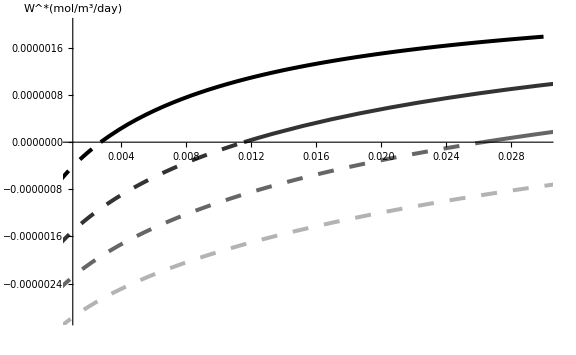
-Graphics-L(m/day)

```mathematica
Labeled[Show[Plot[{W[L,.2Aleak,wmax,1,0.01,kQ]},{L,0.0027213242259699565,0.03},PlotRange->{{0.001,0.03},{-0.000003,0.000002}},PlotStyle->{Black,Thickness[0.005]},AxesStyle->Directive[Black, 20],AxesLabel->{None,Framed[Row[{Style["W^*",Italic],"(mol/",("m")^3,"/day)"}],FrameStyle->None,FrameMargins->10]},(*PlotLegends->Placed[{Row[{"A^L=0.2",,("eq/m")^3}]},{.85,.18}],*)LabelStyle->Directive[Black,20 ],Ticks->{Automatic,Automatic},TicksStyle->{(*Directive[FontOpacity->0,FontSize->0]*)Automatic,Automatic},ImageSize->Large],Plot[{W[L,.2Aleak,wmax,1,0.01,kQ]},{L,0.0001,0.0027213242259699565},PlotStyle->{Black,Thickness[0.005],Dashing[0.02]}],Plot[{W[L,0.5Aleak,wmax,1,0.01,kQ]},{L,0.011546733648089638,0.1},PlotRange->{{0.001,0.03},{-0.000003,0.000002}},PlotStyle->{GrayLevel[0.2],Thickness[0.005]},AxesStyle->Directive[Black, 20],AxesLabel->{None,Framed[Row[{Style["W^*",Italic],"(mol/",("m")^3,"/day)"(*Style["(mol/m^3/day)",Plain]*)}],FrameStyle->None,FrameMargins->10]},(*PlotLegends->Placed[{Row[{"A^L=0.5",,("eq/m")^3}]},{.85,.18}],*)LabelStyle->Directive[Black,20 ]],Plot[{W[L,0.5Aleak,wmax,1,0.01,kQ]},{L,0.0001,0.011546733648089638},AxesStyle->Directive[Black, 20],PlotStyle->{GrayLevel[0.2],Thickness[0.005],Dashing[0.02]}],Plot[{W[L,Aleak,wmax,1,0.01,kQ]},{L,0.02625574935162154,0.1},PlotStyle->{GrayLevel[0.4],Thickness[0.005]},AxesStyle->Directive[Black, 20],(*PlotLegends->Placed[{Row[{"A^L=1",,("eq/m")^3}]},{.85,.18}],*)LabelStyle->Directive[Black,20 ]],Plot[{W[L,Aleak,wmax,1,0.01,kQ]},{L,0.0001,0.02625574935162154},AxesStyle->Directive[Black, 20],PlotStyle->{GrayLevel[0.4],Thickness[0.005],Dashing[0.02]}],
Plot[{W[L,2Aleak,wmax,1,0.01,kQ]},{L,0.05567378075868801,0.1},PlotStyle->{GrayLevel[0.7],Thickness[0.005]},AxesStyle->Directive[Black, 20],AxesStyle->Directive[Black, 20],(*PlotLegends->Placed[{Row[{"A^L=2",,("eq/m")^3}]},{.85,.18}],*)LabelStyle->Directive[Black,20 ]],Plot[{W[L,2Aleak,wmax,1,0.01,kQ]},{L,0.0001,0.05567378075868801},AxesStyle->Directive[Black, 20],PlotStyle->{GrayLevel[0.7],Thickness[0.005],Dashing[0.02]}],ImageSize-> Large],Row[{Style["L",Italic],"(m/day)"}],LabelStyle->Directive[Black, 20]]
```

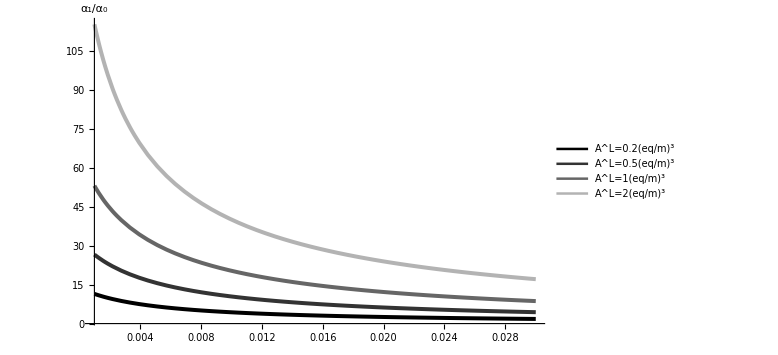
-Graphics-L(m/day)

```mathematica
Labeled[Plot[{α1[x]/α0[x]/.sol1[L,.2Aleak,wmax,Naleak,X2leak,kQ],α1[x]/α0[x]/.sol1[L,.5Aleak,wmax,Naleak,X2leak,kQ],α1[x]/α0[x]/.sol1[L,Aleak,wmax,Naleak,X2leak,kQ],α1[x]/α0[x]/.sol1[L,2Aleak,wmax,Naleak,X2leak,kQ]},{L,0.001,0.03},AxesLabel->{None,Framed[Style["α_1/α_0",Italic],FrameStyle->None,BaseStyle-> {24}]},AxesStyle->Directive[Black, 20],PlotLegends->Placed[{Row[{"A^L=0.2",,("eq/m")^3}],Row[{"A^L=0.5",,("eq/m")^3}],Row[{"A^L=1",,("eq/m")^3}],Row[{"A^L=2",,("eq/m")^3}]},{.85,.75}],LabelStyle->Directive[Black,20 ],PlotStyle->{Directive[Black,Thickness[0.005]],Directive[GrayLevel[0.2],Thickness[0.005]],Directive[GrayLevel[0.4],Thickness[0.005]],Directive[GrayLevel[0.7],Thickness[0.005]]},PlotRange->All,ImageSize->Large],Row[{Style["L",Italic],"(m/day)"}],LabelStyle->Directive[Black, 20]]
```

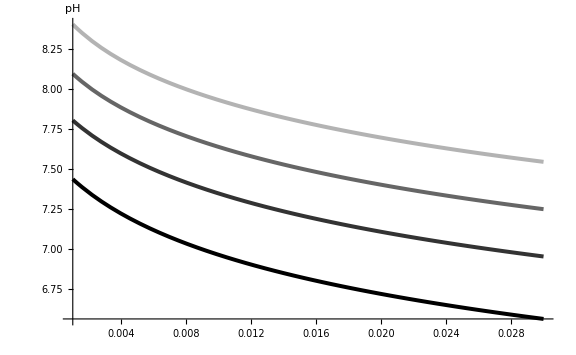
-Graphics-L(m/day)

```mathematica
Labeled[Plot[{pH[L,.2Aleak,wmax,Naleak,X2leak,kQ],pH[L,.5Aleak,wmax,Naleak,X2leak,kQ],pH[L,1Aleak,wmax,Naleak,X2leak,kQ],pH[L,2Aleak,wmax,Naleak,X2leak,kQ]},{L,0.001,0.03},AxesLabel->{None,Framed[Style["pH",Italic],FrameStyle->None,FrameMargins->10,Alignment->Left]},AxesStyle->Directive[Black, 20],PlotStyle->{Directive[Black,Thickness[0.005]],Directive[GrayLevel[0.2],Thickness[0.005]],Directive[GrayLevel[0.4],Thickness[0.005]],Directive[GrayLevel[0.7],Thickness[0.005]]},PlotRange->All,ImageSize->Large,TicksStyle->{Directive[FontOpacity->0,FontSize->0],Automatic}],Row[{Style["L",Italic],"(m/day)"}],LabelStyle->Directive[Black, 20]]
```

```mathematica
alfarat=Table[α1[x]/α0[x]/.sol1[L,a Aleak,wmax,Naleak,X2leak,kQ],{L,0.001,0.1,0.0005},{a,{0.5,1,2}}];
```

```mathematica
Export["alfarL.dat",alfarat]
```

alfarL.dat

```mathematica
A[α λ,Aleak,wmax,Naleak,X2leak,kQ]
pH[α λ,Aleak,wmax,Naleak,X2leak,kQ]
Na[α λ,Aleak,wmax,Naleak,X2leak,kQ]
X2[α λ,Aleak,wmax,Naleak,X2leak,kQ]
Ctleak[α λ,Aleak]
x/.sol1[α λ,Aleak,wmax,Naleak,X2leak,kQ]
```

### Weathering zone (Nonlinear case)

```mathematica
hn[L_,kQ_,β_]:=(L/kQ)^(1/β);
soln[L_,Aleak_,wmax_,Naleak_,X2leak_,kQ_,β_]:=FindRoot[{An==Aleak+(hn[L,kQ,β]wmax)/L(1-α1[x]/(α0[x] Keq)Nan X2n^2),An==Ctleak[L,Aleak](α1[x]+2 α2[x])+Kw/x-x,Nan==Naleak+(hn[L,kQ,β]wmax)/L(1-α1[x]/(α0[x] Keq)Nan X2n^2),X2n==X2leak+2(hn[L,kQ,β]wmax)/L(1-α1[x]/(α0[x] Keq)Nan X2n^2)},{{An,Aleak},{x,Hleak[L,Aleak]},{Nan,Naleak},{X2n,X2leak}}];
An[L_,Aleak_,wmax_,Naleak_,X2leak_,kQ_,β_]:=An/.soln[L,Aleak,wmax,Naleak,X2leak,kQ,β];
pHn[L_,Aleak_,wmax_,Naleak_,X2leak_,kQ_,β_]:=-Log10[x]/.soln[L,Aleak,wmax,Naleak,X2leak,kQ,β];
Nan[L_,Aleak_,wmax_,Naleak_,X2leak_,kQ_,β_]:=Nan/.soln[L,Aleak,wmax,Naleak,X2leak,kQ,β];
X2n[L_,Aleak_,wmax_,Naleak_,X2leak_,kQ_,β_]:=X2n/.soln[L,Aleak,wmax,Naleak,X2leak,kQ,β];
Wn[L_,Aleak_,wmax_,Naleak_,X2leak_,kQ_,β_]:= wmax(1-α1[x]/(α0[x] Keq)Nan[L,Aleak,wmax,Naleak,X2leak,kQ,β] X2n[L,Aleak,wmax,Naleak,X2leak,kQ,β]^2)/.soln[L,Aleak,wmax,Naleak,X2leak,kQ,β]
```

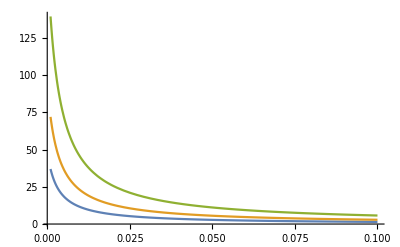

```mathematica
Plot[{α1[x]/α0[x]/.sol1[L,.5Aleak,wmax,Naleak,X2leak,kQ],α1[x]/α0[x]/.sol1[L,Aleak,wmax,Naleak,X2leak,kQ],α1[x]/α0[x]/.sol1[L,2Aleak,wmax,Naleak,X2leak,kQ]},{L,0.001,0.1},PlotRange->All]
```

```mathematica
alfarat=Table[α1[x]/α0[x]/.sol1[L,a Aleak,wmax,Naleak,X2leak,kQ],{L,0.001,0.1,0.0005},{a,{0.5,1,2}}];
```

```mathematica
Export["alfarL.dat",alfarat]
```

alfarL.dat

```mathematica
A[α λ,Aleak,wmax,Naleak,X2leak,kQ]
pH[α λ,Aleak,wmax,Naleak,X2leak,kQ]
Na[α λ,Aleak,wmax,Naleak,X2leak,kQ]
X2[α λ,Aleak,wmax,Naleak,X2leak,kQ]
Ctleak[α λ,Aleak]
x/.sol1[α λ,Aleak,wmax,Naleak,X2leak,kQ]
```

### NAl , Sitl

#### Function of L

Nonlinear

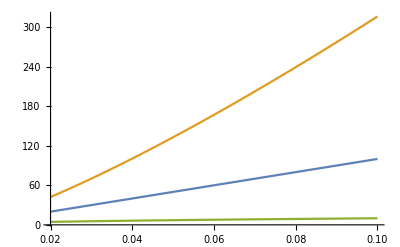

```mathematica
Plot[{hn[L,kQ,1],hn[L,kQ,.8],hn[L,kQ,2]},{L,0.02,0.1},PlotRange->All]
```

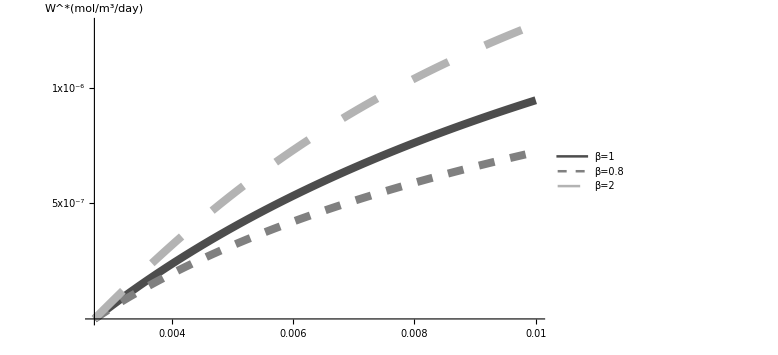
-Graphics-L(m/day)

```mathematica
p1=Labeled[Plot[{Wn[L,.2Aleak,wmax,1,0.01,kQ,1],Wn[L,.2Aleak,wmax,1,0.01,kQ,0.8],Wn[L,.2Aleak,wmax,1,0.01,kQ,2]},{L,0.0027213242259699565,0.01},PlotRange->All,ImageSize-> Large,AxesLabel->{None,Row[{Style["W^*",Italic],"(mol/",("m")^3,"/day)"}]},LabelStyle->Directive[Black, 20],PlotStyle->{Directive[GrayLevel[0.3],Thickness[0.01]],Directive[GrayLevel[0.5],Thickness[0.01],Dashing[0.02]],Directive[GrayLevel[0.7],Thickness[0.01],Dashing[0.05]]},Ticks->{{.004, .006,.008,0.01}, {{5 10^-7,"5x10^-7"},{1 10^-6,"1x10^-6"},{1.5 10^-6,"1.5x10^-6"}}},PlotLegends->Placed[{"β=1","β=0.8","β=2"},{0.85,0.25}]],Row[{Style["L",Italic],"(m/day)"}],LabelStyle->Directive[Black, 25]]
```

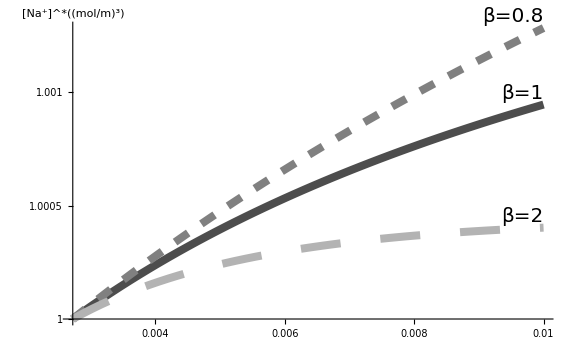

```mathematica
p2=Plot[{Nan[L,.2Aleak,wmax,1,0.01,kQ,1],Nan[L,.2Aleak,wmax,1,0.01,kQ,0.8],Nan[L,.2Aleak,wmax,1,0.01,kQ,2]},{L,0.0027213242259699565,0.01},PlotRange->All,ImageSize-> Large,AxesLabel->{None,Row[{Style["[Na^+]^*",Italic],("(mol/m")^3,")"}]},LabelStyle->Directive[Black, 20],PlotStyle->{Directive[GrayLevel[0.3],Thickness[0.01]],Directive[GrayLevel[0.5],Thickness[0.01],Dashing[0.02]],Directive[GrayLevel[0.7],Thickness[0.01],Dashing[0.05]]},Ticks->{{.004, .006,.008,0.01}, {{1.00,"1"},{1.0005,"1.0005"},{1.001,"1.001"},{1.0015,"1.0015"}}},PlotLabels->Placed[{"β=1","β=0.8","β=2"},Above]]
```

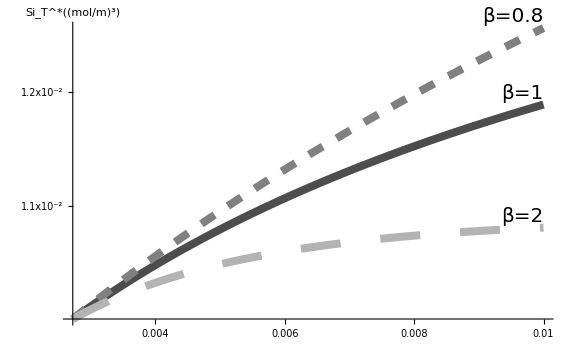

```mathematica
p3=Plot[{X2n[L,.2Aleak,wmax,1,0.01,kQ,1],X2n[L,.2Aleak,wmax,1,0.01,kQ,0.8],X2n[L,.2Aleak,wmax,1,0.01,kQ,2]},{L,0.0027213242259699565,0.01},PlotRange->All,ImageSize-> Large,AxesLabel->{None,Row[{Style["Si_T^*",Italic],("(mol/m")^3,")"}]},LabelStyle->Directive[Black, 20],PlotStyle->{Directive[GrayLevel[0.3],Thickness[0.01]],Directive[GrayLevel[0.5],Thickness[0.01],Dashing[0.02]],Directive[GrayLevel[0.7],Thickness[0.01],Dashing[0.05]]},Ticks->{{.004, .006,.008,0.01}, {{.011,"1.1x10^-2"},{.012,"1.2x10^-2"},{.013,"1.3x10^-2"}}},PlotLabels->Placed[{"β=1","β=0.8","β=2"},Above]]
```

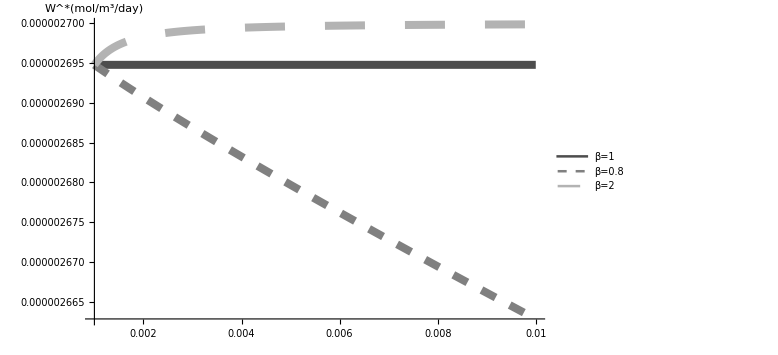
-Graphics-L(m/day)

```mathematica
kc=0;
p4=Labeled[Plot[{Wn[L,.2Aleak,wmax,0,0,kQ,1],Wn[L,.2Aleak,wmax,0,0,kQ,0.8],Wn[L,.2Aleak,wmax,0,0,kQ,2]},{L,0.001,0.01},ImageSize-> Large,AxesLabel->{None,Row[{Style["W^*",Italic],"(mol/",("m")^3,"/day)"}]},LabelStyle->Directive[Black, 20],PlotStyle->{Directive[GrayLevel[0.3],Thickness[0.01]],Directive[GrayLevel[0.5],Thickness[0.01],Dashing[0.02]],Directive[GrayLevel[0.7],Thickness[0.01],Dashing[0.05]]},Ticks->{{0.002,0.004,0.006,0.008,0.01}, Automatic},PlotLegends->Placed[{"β=1","β=0.8","β=2"},{0.85,0.5}]],Row[{Style["L",Italic],"(m/day)"}],LabelStyle->Directive[Black, 25]]
kc=0.1;
```

```mathematica
Export["p1.pdf",p1]
```

p1.pdf

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["p1.pdf"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["p4.pdf"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["p4.pdf"]]]
```

#### Function of Transit Time τ

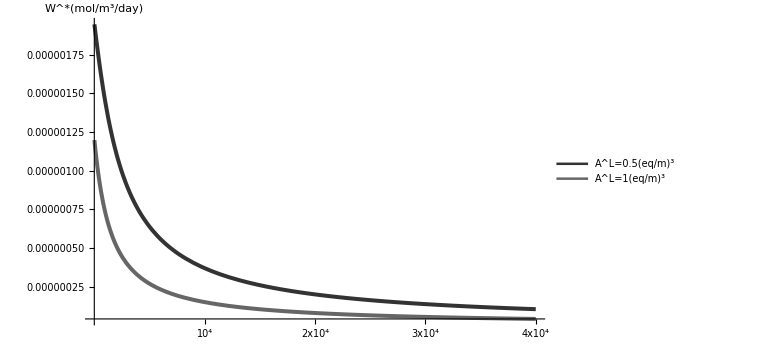
-Graphics-τ(day)

```mathematica
Labeled[Plot[{W[.05,.5Aleak,wmax,1,0.01,1/τ],W[.05,Aleak,wmax,1,0.01,1/τ]},{τ,10,40000},PlotRange->All,PlotStyle->{Directive[GrayLevel[0.2],Thickness[0.005]],Directive[GrayLevel[0.4],Thickness[0.005]]},AxesStyle->Directive[Black, 20],Ticks-> {{{10000,"10^4"},{20000,"2x10^4"},{30000,"3x10^4"},{40000,"4x10^4"}},Automatic},AxesLabel->{None,Framed[Row[{Style["W^*",Italic],"(mol/",("m")^3,"/day)"}],FrameStyle->None,FrameMargins->10]},ImageSize->Large,PlotLegends->Placed[{Row[{Style["A^L=0.5",Italic],,("eq/m")^3}],Row[{Style["A^L=1",Italic],,("eq/m")^3}]},{0.8,0.7}],LabelStyle->Directive[Black,20 ]],Row[{Style["τ",Italic],"(day)"}],LabelStyle->Directive[Black, 20]]
```

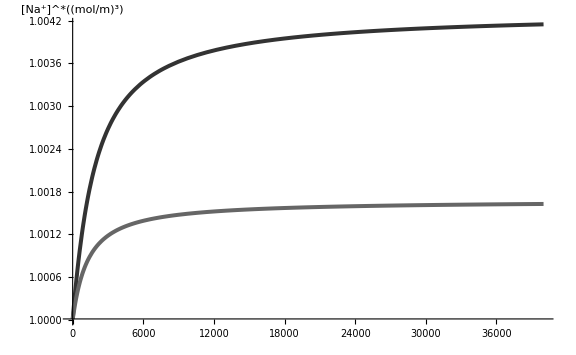

```mathematica
Plot[{Na[0.05,.5Aleak,wmax,1,0.01,1/τ],Na[0.05,Aleak,wmax,1,0.01,1/τ]},{τ,10,40000},PlotStyle->{Directive[GrayLevel[0.2],Thickness[0.005]],Directive[GrayLevel[0.4],Thickness[0.005]]},AxesStyle->Directive[Black, 20],AxesLabel->{None,Framed[Row[{Style["[Na^+]^*",Italic],("(mol/m")^3,")"}],FrameStyle->None,FrameMargins->10]},ImageSize->Large,Ticks->{Automatic, Automatic},TicksStyle->{Directive[FontOpacity->0,FontSize->0],Automatic}]
```

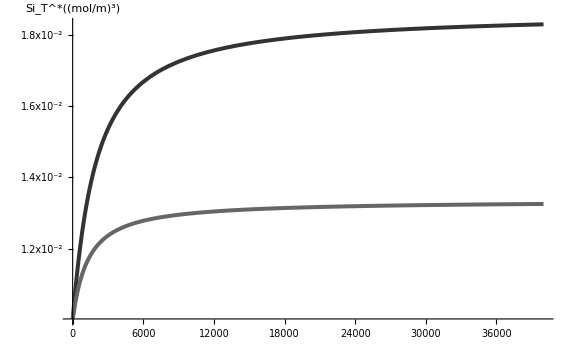

```mathematica
Plot[{X2[0.05,.5Aleak,wmax,1,0.01,1/τ],X2[0.05,Aleak,wmax,1,0.01,1/τ]},{τ,10,40000},PlotRange->All,PlotStyle->{Directive[GrayLevel[0.2],Thickness[0.005]],Directive[GrayLevel[0.4],Thickness[0.005]]},AxesStyle->Directive[Black, 20],AxesLabel->{None,Framed[Row[{Style["Si_T^*",Italic],("(mol/m")^3,")"}],FrameStyle->None,FrameMargins->10]},ImageSize->Large,Ticks->{Automatic,{{0.012,"1.2x10^-2"},{0.014,"1.4x10^-2"},{0.016,"1.6x10^-2"},{0.018,"1.8x10^-2"}}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],Automatic}]
```

```mathematica
Naτ=Table[Nan[.05,Aleak,wmax,1,0.01,k/.FindRoot[(.05/k)^(1/β-1)/k==τ,{k,0.1}],β],{β,{.8,1,2}},{τ,10,50000,10}];//Quiet
```

```mathematica
X2τ=Table[X2n[.05,Aleak,wmax,1,0.01,k/.FindRoot[(.05/k)^(1/β)/(k (.05/k))==τ,{k,0.1}],β],{β,{.8,1,2}},{τ,10,50000,10}];//Quiet
```

```mathematica
Wτ=Table[Wn[.05,Aleak,wmax,1,0.01,k/.FindRoot[(.05/k)^(1/β)/(k (.05/k))==τ,{k,0.1}],β],{β,{.8,1,2}},{τ,10,50000,10}];//Quiet
```

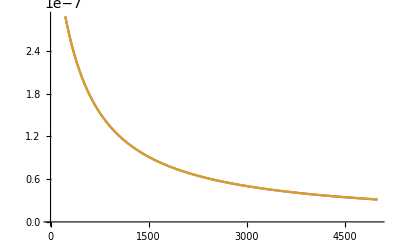

```mathematica
ListLinePlot[{Wτ[[1,All]],Wτ[[2,All]]}]
```

## No Precipitation/Dissolution

```mathematica
(*A=Aleak*)
Hno[L_,A_]:=Last[H/.Quiet[Solve[A==Ctleak[L,A](α1[H]+2 α2[H])+Kw/H-H,{H}]]]
Nano[L_,X2_,A_]:=Last[Nal/.Quiet[Solve[Nal ==Keq α0[Hno[L,A]]/(X2^2 α1[Hno[L,A]]),Nal]]]
pHno[L_,A_]:=-Log10[Hno[L,A]];
```

```mathematica
Nano[α λ,0.01,Aleak]
```

0.281867

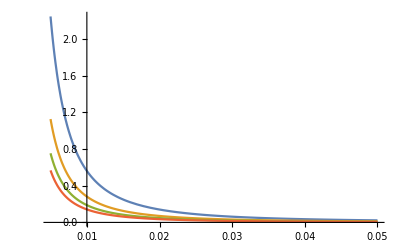

```mathematica
Plot[{Nano[α λ,X2,0.5],Nano[α λ,X2,1],Nano[α λ,X2,1.5],Nano[α λ,X2,2]},{X2,0.005,0.05},PlotRange->All]
```

```mathematica
(*A=Aleak*)
Hno[L_,A_]:=Last[H/.Quiet[Solve[A==Ctleak[L,A](α1[H]+2 α2[H])+Kw/H-H,H]]]
Lno[Na_,X2_,A_]:=Last[L/.Quiet[Solve[1==Keq α0[Hno[L,A]]/(Na X2^2 α1[Hno[L,A]]),L]]]
pHno[L_,A_]:=-Log10[Hno[L,A]];
```

```mathematica
Plot[{Lno[Na,0.01,Aleak](*,Lno[Na,0.01,Aleak],Lno[Na,0.01,1.5Aleak],Lno[Na,0.01,2Aleak]*)},{Na,0.01,1.01}]
```

$Aborted

```mathematica
Lnopd=Table[Lno[1,X2,a Aleak],{X2,0.005,0.02,0.0001},{a,{0.5,1,1.5,2}}];
```

$Aborted

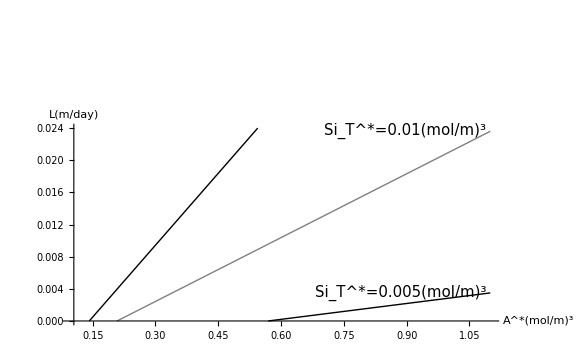

```mathematica
ListLinePlot[{Lno3[[1;;10,1]],Lno3[[1;;10,2]],Lno3[[1;;10,3]]},DataRange->{0.1,1.1},PlotRange->{{0.1,1.1},{0.0,0.024}},ImageSize->Large,AxesStyle->Directive[Black, 20],PlotStyle->{Directive[Black,Thick],Directive[Gray,Thick]},PlotLabels->Placed[{Row[{"Si_T^*=0.005",,("mol/m")^3}],Row[{"Si_T^*=0.01",,("mol/m")^3}],Row[{"Si_T^*=0.015",,("mol/m")^3}]},Right],LabelStyle->Directive[Black, 15],AxesLabel->{Row[{Style["A^*",Italic],("(mol/m)")^3}],Framed[Row[{Style["L",Italic],,"(m/day)"}],FrameStyle->None,FrameMargins->10]}]
```

```mathematica
Lno=Table[Lno[1,X2,a Aleak],{X2,0.005,0.02,0.001},{a,{0.5,1,1.5,2}}];
```

```mathematica
Lno2=Table[Lno[Na,0.01,a Aleak],{Na,0.01,1.01,0.01},{a,{0.5,1,2}}];
```

$Aborted

```mathematica
Lno3=Table[L/.FindRoot[1==Keq α0[Hno[L,A]]/(1 Si^2 α1[Hno[L,A]]),{L,0.005}]//Quiet,{A,0.01,1.51,0.1},{Si,{0.005,0.01,0.015}}];
```

## Simulation

#### General

```mathematica
sim=Quiet[ParametricNDSolve[{hh'[t]==1/n(L-kq hh[t]),ctt'[t]==L/(hh[t] n)(Ctleak[L,aleak]-ctt[t]),Aa'[t]==1/(hh[t] n)(L(aleak-Aa[t])+hh[t]Wr[Aa[t],ctt[t],Naa[t],X22[t]]),Naa'[t]==1/(hh[t] n)(L(naleak-Naa[t])+hh[t]Wr[Aa[t],ctt[t],Naa[t],X22[t]]),X22'[t]==1/(hh[t] n)(L(x2leak-X22[t])+2hh[t]Wr[Aa[t],ctt[t],Naa[t],X22[t]]),hh[0]==0.01,ctt[0]==0,Aa[0]==0,Naa[0]==0,X22[0]==0.0},{hh,ctt,Aa,Naa,X22},{t,0,10000},{L,aleak,naleak,x2leak,kq}]];
```

```mathematica
sim2=Quiet[ParametricNDSolve[{hh'[t]==1/n(L-kq hh[t]),ctt'[t]==L/(hh[t] n)(Ctleak[L,aleak]-ctt[t]),Aa'[t]==1/(hh[t] n)(L(aleak-Aa[t])+hh[t]Wr[Aa[t],ctt[t],Naa[t],X22[t]]),Naa'[t]==1/(hh[t] n)(L(naleak-Naa[t])+hh[t]Wr[Aa[t],ctt[t],Naa[t],X22[t]]),X22'[t]==1/(hh[t] n)(L(x2leak-X22[t])+2hh[t]Wr[Aa[t],ctt[t],Naa[t],X22[t]]),hh[0]==0.01,ctt[0]==0,Aa[0]==0,Naa[0]==2,X22[0]==0.02},{hh,ctt,Aa,Naa,X22},{t,0,10000},{L,aleak,naleak,x2leak,kq}]];
```

#### Function of L

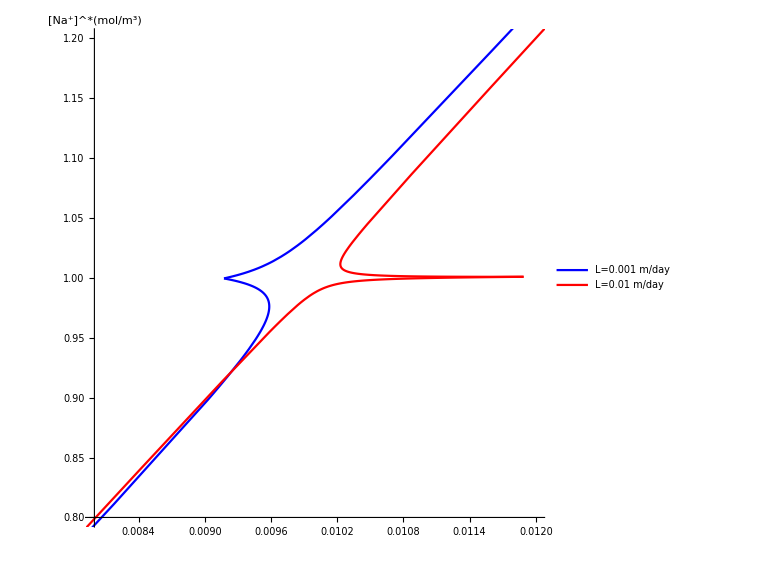
-Graphics-Si_T^*(mol/m^3)

```mathematica
Labeled[Show[ParametricPlot[Evaluate[topplot],{t,0,3000},PlotRange->{{0.008,0.012},{0.8,1.2}},PlotStyle->{Directive[Blue,Thick],Directive[Red,Thick]},AxesStyle->Directive[Black,20],ImageSize->Large,AxesLabel->{(*Framed[Row[{Style["Si_T^*",Italic],"(mol/",("m")^3,")"}],FrameStyle->None,FrameMargins->13]*)None,Framed[Row[{Style["[Na^+]^*",Italic],"(mol/",("m")^3,")"}],FrameStyle->None,FrameMargins->10]},AspectRatio->1/1,LabelStyle->Directive[Black,20],PlotLegends->Placed[{Style["L=0.001",Italic]"m/day",Style["L=0.01",Italic]"m/day"},{0.75,0.2}]],ParametricPlot[Evaluate[topplot2],{t,0,3000},PlotRange->All,PlotStyle->{Directive[Blue,Thick],Directive[Red,Thick]},AspectRatio->1/1.5](*,ListPlot[{{X22[0.001,.2Aleak,1,0.01,kQ][2000],Naa[0.001,.2Aleak,1,0.01,kQ][2000]}/.sim},PlotStyle->Blue,PlotMarkers->{{"*",20}}],ListPlot[{{X22[0.01,.2Aleak,1,0.01,kQ][3000],Naa[0.01,.2Aleak,1,0.01,kQ][3000]}/.sim2},PlotStyle->Red,PlotMarkers->{{"*",20}}]*)],Row[{Style["Si_T^*",Italic],"(mol/",("m")^3,")"}],LabelStyle->Directive[20,Black]]
```

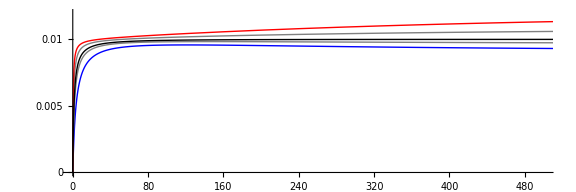

```mathematica
Show[Plot[Evaluate@Table[X22[L,.2Aleak,1,0.01,kQ][t]/.sim,{L,{0.001,0.002,0.005,0.01}}],{t,0,2000},PlotRange->{{0,500},{0.00,0.012}},AspectRatio->1/3,AxesStyle->Directive[Black,20],AxesLabel->{None,None},Ticks->{Automatic,{0,0.005,0.01}},PlotStyle->{Directive[Blue,Thick],Directive[Gray,Thick],Directive[Gray,Thick],Directive[Red,Thick]}],Plot[X22[0.0027213242259699565,.2Aleak,1,0.01,kQ][t]/.sim,{t,0,2000},PlotRange->{{0,500},{0.0,0.012}},PlotStyle->{Black,Thick}],ImageSize->Large]
```

```mathematica
topplot=Table[{X22[l,.2Aleak,1,0.01,kQ][t],Naa[l,.2Aleak,1,0.01,kQ][t]}/.sim,{l,{0.001,0.01}}];
```

```mathematica
topplot2=Table[{X22[l,.2Aleak,1,0.01,kQ][t],Naa[l,.2Aleak,1,0.01,kQ][t]}/.sim2,{l,{0.001,0.01}}];
```

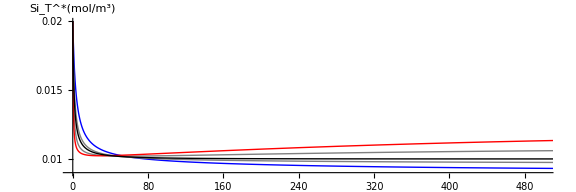

```mathematica
Show[Plot[Evaluate@Table[X22[L,.2Aleak,1,0.01,kQ][t]/.sim2,{L,{0.001,0.002,0.005,0.01}}],{t,0,2000},AspectRatio->1/3,AxesStyle->Directive[Black,20],Ticks->{Automatic,{0.01,0.015,0.02}},TicksStyle->{FontOpacity-> 0,Automatic},AxesLabel->{None,Framed[Row[{Style["Si_T^*",Italic],"(mol/",("m")^3,")"}],FrameStyle->None,FrameMargins->10]},PlotStyle->{Directive[Blue,Thick],Directive[Gray,Thick],Directive[Gray,Thick],Directive[Red,Thick]},PlotRange->{{0,500},{0.009,0.02}}],Plot[X22[0.0027213242259699565,.2Aleak,1,0.01,kQ][t]/.sim2,{t,0,1000},PlotStyle->{Black,Thick},PlotRange->{{0,500},{0.005,0.02}}],ImageSize->Large]
```

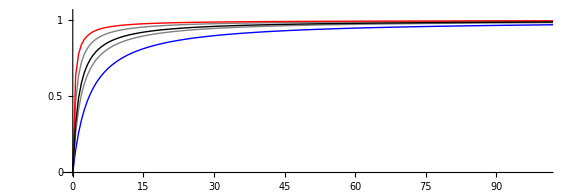

```mathematica
Show[Plot[Evaluate@Table[Naa[L,.2Aleak,1,0.01,kQ][t]/.sim,{L,{0.001,0.002,0.005,0.01}}],{t,0,2000},AspectRatio->1/3,AxesStyle->Directive[Black,20],Ticks->{Automatic,{0,0.5,1}},PlotStyle->{Directive[Blue,Thick],Directive[Gray,Thick],Directive[Gray,Thick],Directive[Red,Thick]},PlotRange->{{0,100},{0,1.05}}],Plot[Naa[0.0027213242259699565,.2Aleak,1,0.01,kQ][t]/.sim,{t,0,2000},PlotStyle->{Black,Thick},PlotRange->{{0,100},{0,1.05}}],ImageSize->Large]
```

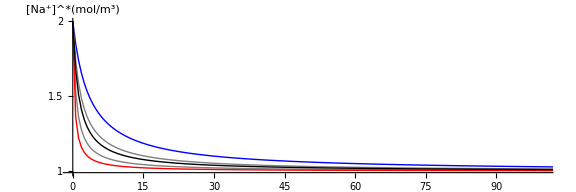

```mathematica
Show[Plot[Evaluate@Table[Naa[L,.2Aleak,1,0.01,kQ][t]/.sim2,{L,{0.001,0.002,0.005,0.01}}],{t,0,2000},AspectRatio->1/3,AxesStyle->Directive[Black,20],LabelStyle->Directive[Black,20],TicksStyle->{FontOpacity-> 0,Automatic},Ticks->{Automatic,{1,1.5,2}},AxesLabel->{None,Framed[Row[{Style["[Na^+]^*",Italic],"(mol/",("m")^3,")"}],FrameStyle->None,FrameMargins->10]},PlotStyle->{Directive[Blue,Thick],Directive[Gray,Thick],Directive[Gray,Thick],Directive[Red,Thick]},PlotRange->{{0,100},{0.99,2}},PlotLegends->Placed[{Row[{Style["L=0.001",Italic],,"m/day"}],None,None,Row[{Style["L=0.01",Italic],,"m/day"}]},Center]],Plot[Naa[0.0027213242259699565,.2Aleak,1,0.01,kQ][t]/.sim2,{t,0,2000},LabelStyle->Directive[Black,20],PlotStyle->{Black,Thick},PlotRange->{{0,500},{0.95,2}},PlotLegends->Placed[{Row[{Style["L=L^*=0.0027",Italic],,"m/day"}]},Center]],ImageSize->Large]
```

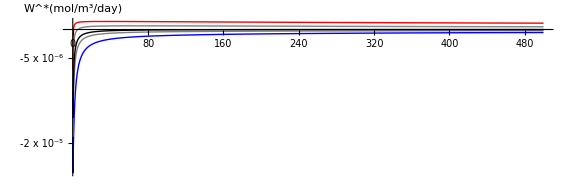

```mathematica
Show[Plot[Evaluate@Table[Wr[Aa[L,.2Aleak,1,0.01,kQ][t],ctt[L,.2Aleak,1,0.01,kQ][t],Naa[L,.2Aleak,1,0.01,kQ][t],X22[L,.2Aleak,1,0.01,kQ][t]]/.sim2,{L,{0.001,0.002,0.005,0.01}}],{t,0,500},TicksStyle->{FontOpacity-> 0,Automatic},AxesLabel->{None,Framed[Row[{Style["W^*",Italic],"(mol/",("m")^3,"/day)"}],FrameStyle->None,FrameMargins->10]},AspectRatio->1/3,Ticks->{Automatic,{{-2 10^-5,"-2 x 10^-5"},{- 5 10^-6,"-5 x 10^-6"}}},AxesStyle->Directive[Black,20],PlotStyle->{Directive[Blue,Thick],Directive[Gray,Thick],Directive[Gray,Thick],Directive[Red,Thick]},PlotRange->All,ImageSize->Large],Plot[Evaluate@Table[Wr[Aa[L,.2Aleak,1,0.01,kQ][t],ctt[L,.2Aleak,1,0.01,kQ][t],Naa[L,.2Aleak,1,0.01,kQ][t],X22[L,.2Aleak,1,0.01,kQ][t]]/.sim2,{L,{0.0027213242259699565}}],{t,0,500},PlotStyle->{Black,Thick},PlotRange->All,ImageSize->Large]]
```

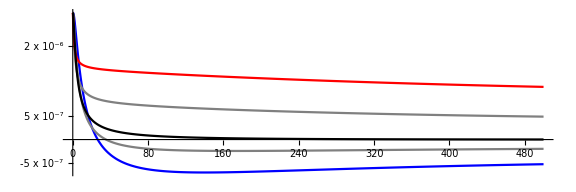
-Graphics-t(days)

```mathematica
Labeled[Show[Plot[Evaluate@Table[Wr[Aa[L,.2Aleak,1,0.01,kQ][t],ctt[L,.2Aleak,1,0.01,kQ][t],Naa[L,.2Aleak,1,0.01,kQ][t],X22[L,.2Aleak,1,0.01,kQ][t]]/.sim,{L,{0.001,0.002,0.005,0.01}}],{t,0,500},Ticks->{Automatic,{{-5 10^-7,"-5 x 10^-7"},{5 10^-7,"5 x 10^-7"},{2 10^-6,"2 x 10^-6"}}},AspectRatio->1/3,AxesStyle->Directive[Black,20],PlotStyle->{Directive[Blue,Thick],Directive[Gray,Thick],Directive[Gray,Thick],Directive[Red,Thick]},PlotRange->All,ImageSize->Large],Plot[Evaluate@Table[Wr[Aa[L,.2Aleak,1,0.01,kQ][t],ctt[L,.2Aleak,1,0.01,kQ][t],Naa[L,.2Aleak,1,0.01,kQ][t],X22[L,.2Aleak,1,0.01,kQ][t]]/.sim,{L,{0.0027213242259699565}}],{t,0,500},PlotStyle->{Black,Thick},PlotRange->All,ImageSize->Large]],Row[{Style["t",Italic],"(days)"}],LabelStyle->{Black,20}]
```

```mathematica
(*Exporting*)
NasimL1=Table[Naa[L,.2Aleak,1,0.01,kQ][t]/.sim,{t,0,1000,0.1},{L,{0.001,0.005,0.01,0.026255751802357195,0.05,0.1,0.5}}];
NasimL2=Table[Naa[L,.2Aleak,1,0.01,kQ][t]/.sim2,{t,0,1000,0.1},{L,{0.001,0.005,0.01,0.026255751802357195,0.05,0.1,0.5}}];
X2simL1=Table[X22[L,.2Aleak,1,0.01,kQ][t]/.sim,{t,0,1000,0.1},{L,{0.001,0.005,0.01,0.026255751802357195,0.05,0.1,0.5}}];
X2simL2=Table[X22[L,.2Aleak,1,0.01,kQ][t]/.sim2,{t,0,1000,0.1},{L,{0.001,0.005,0.01,0.026255751802357195,0.05,0.1,0.5}}];
(*WsimL1=Table[Wr[Aa[L,Aleak,1,0.01,kQ][t],ctt[L,Aleak,1,0.01,kQ][t],Naa[L,Aleak,1,0.01,kQ][t],X22[L,Aleak,1,0.01,kQ][t]]/.sim,{t,0,500},{L,{0.001,0.005,0.01,0.026255751802357195,0.05,0.1,0.5}}];
WsimL2=Table[Wr[Aa[L,Aleak,1,0.01,kQ][t],ctt[L,Aleak,1,0.01,kQ][t],Naa[L,Aleak,1,0.01,kQ][t],X22[L,Aleak,1,0.01,kQ][t]]/.sim2,{t,0,500},{L,{0.001,0.005,0.01,0.026255751802357195,0.05,0.1,0.5}}];*)
Export["NasimL1.dat",NasimL1];
Export["NasimL2.dat",NasimL2];
Export["X2simL1.dat",X2simL1];
Export["X2simL2.dat",X2simL2];
(*Export["WsimL1.dat",WsimL1];
Export["WsimL2.dat",WsimL2];*)
```

```mathematica
hsimL1=Table[hh[L,Aleak,1,0.01,kQ][t]/.sim,{t,0,1000,0.1},{L,{0.001,0.5}}];
hsimL2=Table[hh[L,Aleak,1,0.01,kQ][t]/.sim2,{t,0,1000,0.1},{L,{0.001,0.5}}];
```

```mathematica
Export["hsimL1.dat",hsimL1];
Export["hsimL2.dat",hsimL2];
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["hsimL1.dat"]]]
```

```mathematica
Export["X2simL2.dat",X2simL2];
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["X2simL2.dat"]]]
```

#### Function of τ

```mathematica
topplot3=Table[{X22[0.005,.2Aleak,1,0.01,k][t],Naa[0.005,.2Aleak,1,0.01,kQ][t]}/.sim,{k,{0.0001,1}}];
topplot4=Table[{X22[0.005,.2Aleak,1,0.01,k][t],Naa[0.005,.2Aleak,1,0.01,kQ][t]}/.sim2,{k,{0.0001,1}}];
```

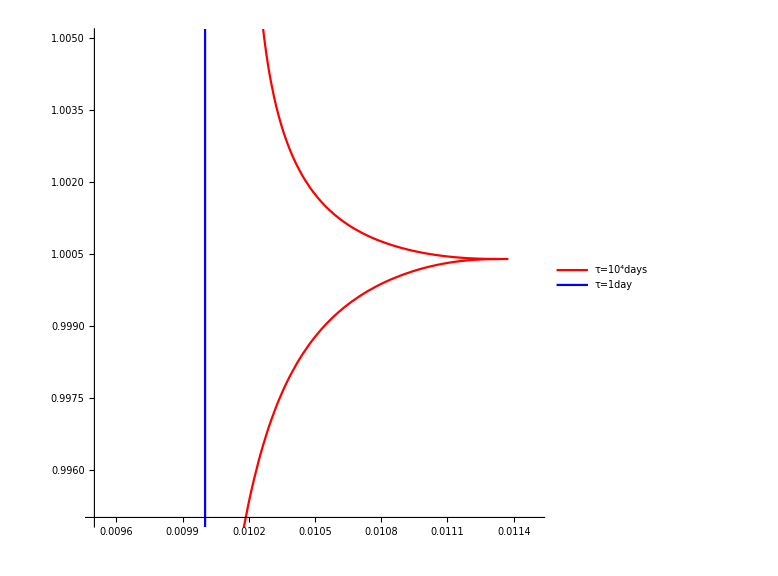
-Graphics-Si_T^*(mol/m^3)

```mathematica
Labeled[Show[ParametricPlot[Evaluate[topplot3],{t,0,4000},PlotRange->{{0.0095,0.0115},{0.995,1.005}},PlotStyle->{Directive[Red,Thick],Directive[Blue,Thick]},AxesStyle->Directive[Black,20],ImageSize->Large,AxesLabel->{(*Framed[Row[{Style["Si_T^*",Italic],"(mol/",("m")^3,")"}],FrameStyle->None,FrameMargins->20]*)None,(*Framed[Row[{Style["[Na^+]^*",Italic],"(mol/",("m")^3,")"}],FrameStyle->None,FrameMargins->10]*)None},AspectRatio->1/1,LabelStyle->Directive[Black,20],PlotLegends->Placed[{Row[{Style["τ=10^4",Italic],,"days"}],Row[{Style["τ=1",Italic],,"day"}]},{0.75,0.2}]],ParametricPlot[Evaluate[topplot4],{t,0,3000},PlotRange->All,PlotStyle->{Directive[Red,Thick],Directive[Blue,Thick]},AspectRatio->1/1.5](*,ListPlot[{{X22[0.005,.2Aleak,1,0.01,.0001][4000],Naa[0.005,.2Aleak,1,0.01,0.0001][4000]}/.sim},PlotStyle->Blue,PlotMarkers->{{"*",20}}],ListPlot[{{X22[0.005,.2Aleak,1,0.01,1][3000],Naa[0.005,.2Aleak,1,0.01,1][3000]}/.sim2},PlotStyle->Red,PlotMarkers->{{"x",20}}]*)],Row[{Style["Si_T^*",Italic],"(mol/",("m")^3,")"}],LabelStyle->Directive[20,Black]]
```

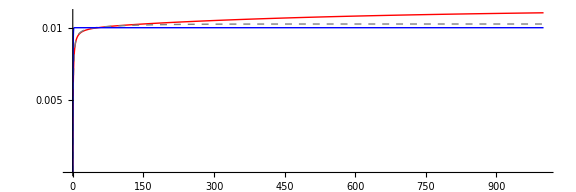

```mathematica
Show[Plot[Evaluate@Table[{X22[0.005,.2Aleak,1,0.01,kQ][t]/.sim},{kQ,{0.0001,0.005,1}}],{t,0,1000},PlotRange->All,AspectRatio->1/3,ImageSize->Large,AxesStyle-> Directive[20,Black],Ticks->{Automatic,{0.005,0.01}},PlotStyle->{Directive[Red,Thick],Directive[Gray,Thick,Dashed],Directive[Blue,Thick]}]]
```

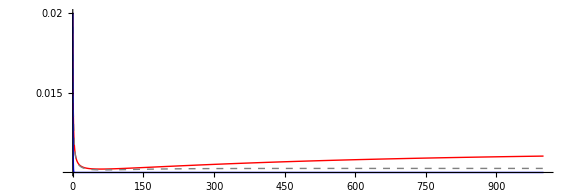

```mathematica
Show[Plot[Evaluate@Table[{X22[0.005,.2Aleak,1,0.01,kQ][t]/.sim2},{kQ,{0.0001,0.005,1}}],{t,0,1000},PlotRange->All,AspectRatio->1/3,ImageSize->Large,TicksStyle->{FontOpacity-> 0,Automatic},Ticks->{Automatic,{0.015,0.02}},AxesStyle-> Directive[20,Black],PlotStyle->{Directive[Red,Thick],Directive[Gray,Thick,Dashed],Directive[Blue,Thick]}]]
```

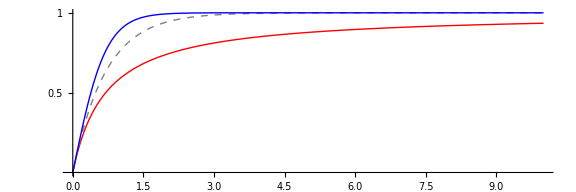

```mathematica
Show[Plot[Evaluate@Table[{Naa[0.005,.2Aleak,1,0.01,kQ][t]/.sim},{kQ,{0.00001,0.5,1}}],{t,0,10},PlotRange->All,AspectRatio->1/3,ImageSize->Large,AxesStyle-> Directive[20,Black],Ticks->{Automatic,{0.5,1}},PlotStyle->{Directive[Red,Thick],Directive[Gray,Thick,Dashed],Directive[Blue,Thick]}]]
```

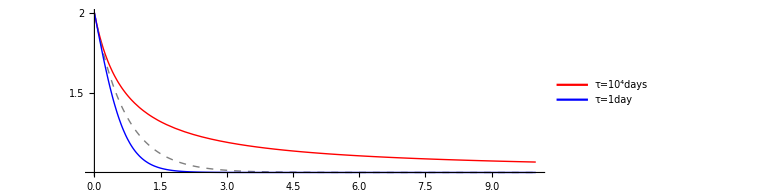

```mathematica
Show[Plot[Evaluate@Table[{Naa[0.005,.2Aleak,1,0.01,kQ][t]/.sim2},{kQ,{0.0001,0.5,1}}],{t,0,10},PlotRange->All,AspectRatio->1/3,ImageSize->Large,AxesStyle-> Directive[20,Black],TicksStyle->{FontOpacity-> 0,Automatic},LabelStyle->Directive[Black,20],PlotLegends->Placed[{Row[{"τ=10^4","days"}],None,Row[{"τ=1","day"}]},Center],Ticks->{Automatic,{1.5,2}},PlotStyle->{Directive[Red,Thick],Directive[Gray,Thick,Dashed],Directive[Blue,Thick]}]]
```

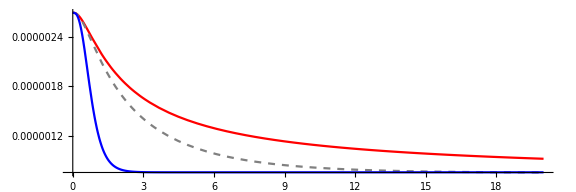
-Graphics-t(days)

```mathematica
Labeled[Plot[Evaluate@Table[Wr[Aa[0.005,.2Aleak,1,0.01,kQ][t],ctt[0.005,.2Aleak,1,0.01,kQ][t],Naa[0.005,.2Aleak,1,0.01,kQ][t],X22[0.005,.2Aleak,1,0.01,kQ][t]]/.sim,{kQ,{0.0001,0.1,1}}],{t,0,20},PlotRange->All,ImageSize->Large,AspectRatio->1/3,ImageSize->Large,AxesStyle-> Directive[20,Black],PlotStyle->{Directive[Red,Thick],Directive[Gray,Thick,Dashed],Directive[Blue,Thick]}],Row[{Style["t",Italic],"(days)"}],LabelStyle->{Black,20}]
```

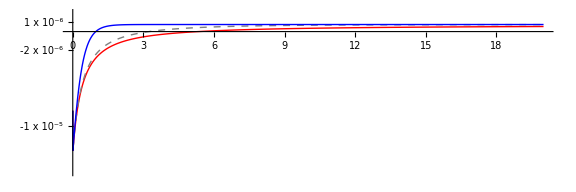

```mathematica
Plot[Evaluate@Table[Wr[Aa[0.005,.2Aleak,1,0.01,kQ][t],ctt[0.005,.2Aleak,1,0.01,kQ][t],Naa[0.005,.2Aleak,1,0.01,kQ][t],X22[0.005,.2Aleak,1,0.01,kQ][t]]/.sim2,{kQ,{0.00001,0.1,1}}],{t,0,20},PlotRange->{{0,20},{-1.5 10^-5,2 10^-6}},TicksStyle->{FontOpacity-> 0,Automatic},Ticks->{Automatic,{{-1 10^-5,"-1 x 10^-5"},{- 2 10^-6,"-2 x 10^-6"},{1 10^-6,"1 x 10^-6"}}},ImageSize->Large,AspectRatio->1/3,ImageSize->Large,AxesStyle-> Directive[20,Black],PlotStyle->{Directive[Red,Thick],Directive[Gray,Thick,Dashed],Directive[Blue,Thick]}]
```

```mathematica
Na2simk1=Table[Naa[0.05,Aleak,1,0.01,kQ][t]/.sim,{t,0,10000},{kQ,{0.001,0.5,1}}];
Na2simk2=Table[Naa[0.05,Aleak,1,0.01,kQ][t]/.sim2,{t,0,10000},{kQ,{0.001,0.5,1}}];
X22simk1=Table[X22[0.05,Aleak,1,0.01,kQ][t]/.sim,{t,0,10000},{kQ,{0.001,0.005,1}}];
X22simk2=Table[X22[0.05,Aleak,1,0.01,kQ][t]/.sim2,{t,0,10000},{kQ,{0.001,0.005,1}}];
(*Wsimk1=Table[Wr[Aa[0.05,Aleak,1,0.01,kQ][t],ctt[0.05,Aleak,1,0.01,kQ][t],Naa[0.05,Aleak,1,0.01,kQ][t],X22[0.05,Aleak,1,0.01,kQ][t]]/.sim,{t,0,20,0.1},{kQ,{0.001,0.1,1}}];
Wsimk2=Table[Wr[Aa[0.05,Aleak,1,0.01,kQ][t],ctt[0.05,Aleak,1,0.01,kQ][t],Naa[0.05,Aleak,1,0.01,kQ][t],X22[0.05,Aleak,1,0.01,kQ][t]]/.sim2,{t,0,20,0.05},{kQ,{0.001,0.1,1}}];*)
```

```mathematica
hsimk1=Table[hh[0.05,Aleak,1,0.01,kQ][t]/.sim,{t,0,10000},{kQ,{0.001,1}}];
hsimk2=Table[hh[0.05,Aleak,1,0.01,kQ][t]/.sim2,{t,0,10000},{kQ,{0.001,1}}];
```

```mathematica
Export["hsimk1.dat",hsimk1];
Export["hsimk2.dat",hsimk2];
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["hsimk1.dat"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["hsimk1.dat"]]]
```

```mathematica
Export["X2simk1.dat",X22simk1];
Export["X2simk2.dat",X22simk2];
Export["Nasimk1.dat",Na2simk1];
Export["Nasimk2.dat",Na2simk2];
(*Export["Wsimk1.dat",Wsimk1];
Export["Wsimk2.dat",Wsimk2];*)
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["X2simk1.dat"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Wsimk2.dat"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Wsimk1.dat"]]]
```

## Data

### New Data

```mathematica
Clear[datawhite]
datawhite={{225,133},{1010,989},{1240,930},{1040,728},{3668,1534},{1051,608},{1395,1201},{875,130},{870,166},{2464,1489},{2135,1539},{2185,1004},{1410,392},{2824,1896},{1507,401}};
datawhite[[All,1]]=datawhite[[All,1]]*0.001;
datawhite[[All,2]]=datawhite[[All,2]]*10^2;
```

```mathematica
Clear[datawhite1]
datawhite1={{209,133},{909,989},{1128,930},{936,728},{3264,1534},{977,608},{1284,1201},{814,130},{809,166},{2242,1489},{1943,1539},{1988,1004},{1297,392},{2541,1896}};
datawhite1[[All,1]]=datawhite1[[All,1]]*0.001;
datawhite1[[All,2]]=datawhite1[[All,2]]*10^2;
```

```mathematica
taus1=Table[{Quiet[FindRoot[X2[datawhite1[[i,1]]/365,Aleak,wmax,1,0.02,1/a]*datawhite1[[i,1]]*10^6==datawhite1[[i,2]],{a,1000}]],datawhite1[[i,2]]},{i,1,Length[datawhite1]}];
```

```mathematica
Quiet[FindRoot[X2n[datawhite1[[i,1]]/365,Aleak,wmax,1,0.02,1/a,]*datawhite1[[i,1]]*10^6==datawhite1[[i,2]],{a,1000}]]
```

```mathematica
Quiet[FindRoot[X2[datawhite1[[i,1]]/365,Aleak,wmax,1,0.02,1/a]*datawhite1[[i,1]]*10^6==datawhite1[[i,2]],{a,1000}]]/.i-> 5
```

{a→5425.68}

```mathematica
Quiet[FindRoot[X2[datawhite[[i,1]]/365,Aleak,wmax,1,0.02,1/a]*datawhite[[i,1]]*10^6==datawhite[[i,2]],{a,1000}]]/.i-> 5
```

{a→11501.}

```mathematica
taus1
```

{{{a→80855.2},13300},{{a→5.62433×10^8},98900},{{a→3.00772×10^9},93000},{{a→4.71049×10^9},72800},{{a→5425.68},153400},{{a→16963.},60800},{{a→1.31434×10^9},120100},{{a→-755.767},13000},{{a→98.4127},16600},{{a→13205.3},148900},{{a→53878.8},153900},{{a→6694.49},100400},{{a→1990.68},39200},{{a→18949.2},189600}}

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["taus.dat"]]]
```

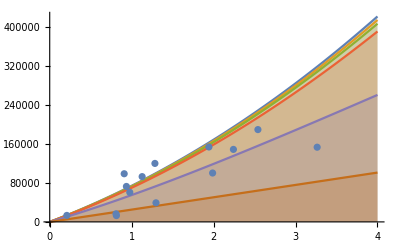

```mathematica
Show[Quiet[Plot[Evaluate@Table[X2[Ly/365,Aleak,wmax,1,0.02,a kQ]*Ly*10^6,{a,{0.001,.05,.1,.2,1,10}}],{Ly,0.01,4},Filling->Axis]],ListPlot[{(*data2,*)datawhite1}]](*Keq=1;*)
```

```mathematica
1/(.1 kQ)
```

10000.

```mathematica
1/kQ
```

1000.

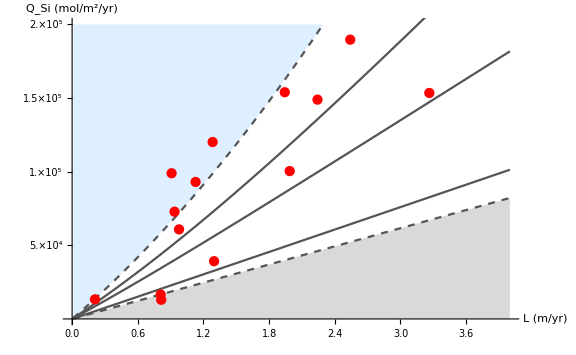
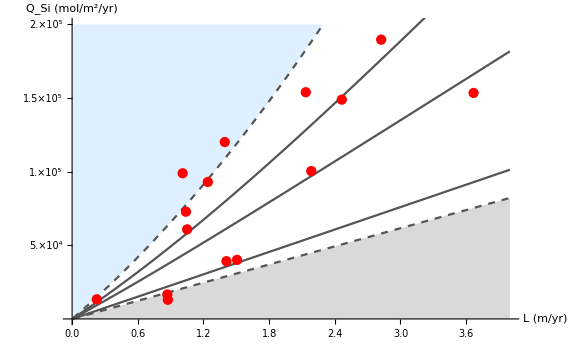

```mathematica
Keq=10^0;
Row[{Show[Plot[{500000,Evaluate@Table[X2[Ly/365,Aleak,wmax,1,0.02,a kQ]*Ly*10^6,{a,{.001}}]},{Ly,0.01,4},PlotRange->{{0,4},{0,200000}},AxesLabel->{Framed["L (m/yr)",FrameStyle->None,FrameMargins->10],Framed["Q_Si (mol/m^2/yr)",FrameStyle->None,FrameMargins->10]},AxesStyle->Directive[Black, 15],PlotStyle->Directive[Darker[Gray],Thick,Dashed],Filling->{1->{{2},LightBlue}},Ticks->{Automatic,{{50000,ScientificForm[50000.,1]},{100000, ScientificForm[100000.,1]},{150000,ScientificForm[150000.,2]},{200000.,ScientificForm[200000.,2]}}}]//Quiet,Plot[{Evaluate@Table[X2[Ly/365,Aleak,wmax,1,0.02,a kQ]*Ly*10^6,{a,{10}}]},{Ly,0.01,4},Filling->Axis,FillingStyle->LightGray,PlotStyle->Directive[Darker[Gray],Thick,Dashed]]//Quiet,Quiet[Plot[Evaluate@Table[X2[Ly/365,Aleak,wmax,1,0.02,a kQ]*Ly*10^6,{a,{.1,.2,1}}],{Ly,0.01,4},PlotStyle->Directive[Darker[Gray],Thick]]],ListPlot[{datawhite1},PlotStyle->Directive[Red]],ImageSize->Large],Show[Plot[{500000,Evaluate@Table[X2[Ly/365,Aleak,wmax,1,0.02,a kQ]*Ly*10^6,{a,{.001}}]},{Ly,0.01,4},PlotRange->{{0,4},{0,200000}},AxesLabel->{Framed["L (m/yr)",FrameStyle->None,FrameMargins->10],Framed["Q_Si (mol/m^2/yr)",FrameStyle->None,FrameMargins->10]},AxesStyle->Directive[Black, 15],PlotStyle->Directive[Darker[Gray],Thick,Dashed],Filling->{1->{{2},LightBlue}},Ticks->{Automatic,{{50000,ScientificForm[50000.,1]},{100000, ScientificForm[100000.,1]},{150000,ScientificForm[150000.,2]},{200000.,ScientificForm[200000.,2]}}}]//Quiet,Plot[{Evaluate@Table[X2[Ly/365,Aleak,wmax,1,0.02,a kQ]*Ly*10^6,{a,{10}}]},{Ly,0.01,4},Filling->Axis,FillingStyle->LightGray,PlotStyle->Directive[Darker[Gray],Thick,Dashed]]//Quiet,Quiet[Plot[Evaluate@Table[X2[Ly/365,Aleak,wmax,1,0.02,a kQ]*Ly*10^6,{a,{.1,.2,1}}],{Ly,0.01,4},PlotStyle->Directive[Darker[Gray],Thick]]],ListPlot[{datawhite},PlotStyle->Directive[Red]],ImageSize->Large]}]
Keq=10^-3;
```

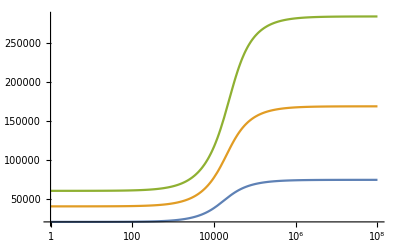

```mathematica
LogLinearPlot[{X2[1/365,Aleak,wmax,1,0.02,1/τ]*1*10^6,X2[2/365,Aleak,wmax,1,0.02,1/τ]*2*10^6,X2[3/365,Aleak,wmax,1,0.02,1/τ]*3*10^6},{τ,1,10^8},PlotRange->All]
```

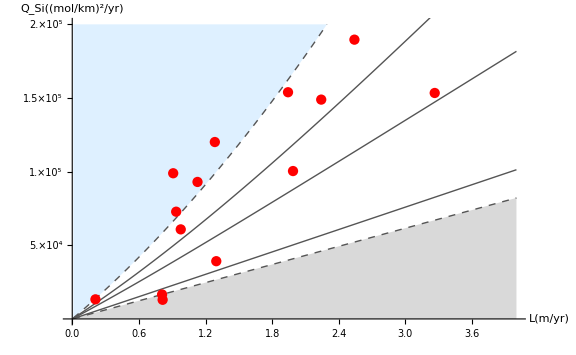

```mathematica
Keq=1;
Show[Plot[{500000,Evaluate@Table[X2[Ly/365,Aleak,wmax,1,0.02,a kQ]*Ly*10^6,{a,{.001}}]},{Ly,0.01,4},PlotRange->{{0,4},{0,200000}},AxesLabel->{Framed[Row[{Style["L" ,Italic],,"(m/yr)"}],FrameStyle->None,FrameMargins->10],Framed[Row[{Style["Q_Si",Italic],("(mol/km")^2,"/yr)"}],FrameStyle->None,FrameMargins->10]},AxesStyle->Directive[Black, 15],PlotStyle->Directive[Darker[Gray],Thick,Dashed],Filling->{1->{{2},LightBlue}},Ticks->{Automatic,{{50000,ScientificForm[50000.,1]},{100000, ScientificForm[100000.,1]},{150000,ScientificForm[150000.,2]},{200000.,ScientificForm[200000.,2]}}}]//Quiet,Plot[{Evaluate@Table[X2[Ly/365,Aleak,wmax,1,0.02,a kQ]*Ly*10^6,{a,{10}}]},{Ly,0.01,4},Filling->Axis,FillingStyle->LightGray,PlotStyle->Directive[Darker[Gray],Thick,Dashed]]//Quiet,Quiet[Plot[Evaluate@Table[X2[Ly/365,Aleak,wmax,1,0.02,a kQ]*Ly*10^6,{a,{.1,.2,1}}],{Ly,0.01,4},PlotStyle->Directive[Darker[Gray],Thick]]],ListPlot[{datawhite1},PlotStyle->Directive[Red]],ImageSize->Large]
Keq=10^-3;
```

## Soil Moisture Model

```mathematica
(*Soil Parameters*)
zr=20;
b=4.38;
c=11.7;
Ks=100;
n=0.42;
be=2 b+4;
(*Soil moisture thresholds*)
sh=0.08;
sw=0.11;
ss=0.31;
sf=0.52;
(*Evapotranspiration parameters*)
Ew=0.01;
Em=0.45;
(*Rainfall Parameters*)
delta=0.;
αr=2;
λ=0.2;
λp[λ_]:=λ Exp[-delta 1/αr];
(*Normalized Parameters*)
γ=(n zr)/αr;
η=Em/(n zr);
ηw=Ew/(n zr);
m=Ks/(n zr(Exp[be(1-sf)]-1));
```

```mathematica
(*Soil Moisture pdf*)
𝒟[λ_,Em_,zr_]:=ProbabilityDistribution[{"PDF",Piecewise[{{1/(Ew/(n zr))((s-sh)/(sw-sh))^((λ Exp[-delta 1/αr](sw-sh))/(Ew/(n zr))-1)Exp[-(n zr)/αr s], sh<s≤sw}, {1/(Ew/(n zr))(1+((Em/(n zr))/(Ew/(n zr))-1)((s-sw)/(ss-sw)))^((λ Exp[-delta 1/αr](ss-sw))/(Em/(n zr)-Ew/(n zr))-1)Exp[-(n zr)/αr s], sw<s≤ss}, {1/(Em/(n zr))Exp[-(n zr)/αr s+(λ Exp[-delta 1/αr] (s-ss))/(Em/(n zr))]((Em/(n zr))/(Ew/(n zr)))^((λ Exp[-delta 1/αr](ss-sw))/(Em/(n zr)-Ew/(n zr))), ss<s≤sf}, {1/(Em/(n zr))Exp[-(be+(n zr)/αr)s+be sf]((Em/(n zr)Exp[be s])/((Em/(n zr)-Ks/(n zr (Exp[be(1-sf)]-1)))Exp[be sf]+Ks/(n zr (Exp[be(1-sf)]-1)) Exp[be s]))^((λ Exp[-delta 1/αr])/(be(Em/(n zr)-Ks/(n zr (Exp[be(1-sf)]-1))))+1)((Em/(n zr))/(Ew/(n zr)))^((λ Exp[-delta 1/αr](ss-sw))/(Em/(n zr)-Ew/(n zr)))Exp[(λ Exp[-delta 1/αr](sf-ss))/(Em/(n zr))], sf<s≤1}}]},{s,sh,1},Method->"Normalize"];
p[x_,λ_,Em_,zr_]:=PDF[𝒟[λ,Em,zr],x];
P[x_,λ_,Em_,zr_]:=CDF[𝒟[λ,Em,zr],x];
(*Plot[p[s,λp,Em,zr],{s,sh,1},PlotRange->{{0,1},{0,10}}]*)
```

```mathematica
(*Mean Water Balance*)
Ev[λ_,Em_,zr_]:=αr λp[λ] P[ss,λ,Em,zr]-αr Em/(n zr) p[ss,λ,Em,zr]+Em(1-P[ss,λ,Em,zr])
(*L[λ_,Em_,zr_]:=αr(λp[λ]-λp[λ] P[sf,λ,Em,zr]-(Em/(n zr)+Ks/(n zr))p[1,λ,Em,zr]+Em/(n zr) p[sf,λ,Em,zr])-Em(1-P[sf,λ,Em,zr])*) (*Maybe wrong in the paper*)
Q[λ_,Em_,zr_]:=αr λ-Ev[λ,Em,zr]-Int[λ,Em,zr]-L[λ,Em,zr]
Int[λ_,Em_,zr_]:=αr (λ-λp[λ])
L[λ_,Em_,zr_]:=n zr NIntegrate[p[s,λ,Em,zr]*Ks/(n zr(Exp[be(1-sf)]-1))*(Exp[be*(s-sf)]-1),{s,sf,1}]
(*Note that the above values are not normalized. They need to be divided by the mean rainfall αrλ to obtain the %*)
```

```mathematica
r=98.4;
etm=0.03;
λλ=r/(365αr);
l=L[λλ,etm,30]
l/(l+Q[λλ,etm,30])
```

```mathematica
0.22338167657273514 365
```

81.5343

```mathematica
Table[{l=L[r/(365αr),etm,30],L[r/(365αr),etm,30]/(L[r/(365αr),etm,30]+Q[r/(365αr),etm,30])},{r,{98.4,95.9,183.0,330.,50.8,214.6,214.6,214.6,454.1,115.3,200.,286.1,270.7,282.2}},{etm,{0.03,0.024,0.12,0.13,0.1,0.33,0.25,0.32,0.24,0.029,0.1,0.11,0.17,0.17}}]
```

```mathematica
A={{{0.22338167657273514,0.9323534184060295},{0.22912693209194432,0.932968876311145},{0.14202091129203184,0.9250270888612924},{0.13437529012865532,0.9243439682325958},{0.1585003306451323,0.9264512589230965},{0.05389782774533879,0.9131433376946005},{0.07342399422994246,0.9171927757149296},{0.05580541317936259,0.913626770279208},{0.07672613386583281,0.9177317844941744},{0.22433824663166926,0.9324540991719722},{0.1585003306451323,0.9264512589230965},{0.15007367319092613,0.9257289066752094},{0.10809020966785246,0.9217702094284373},{0.10809020966785246,0.9217702094284373}},{{0.21706493454689627,0.9326508913086337},{0.22280935545792357,0.933273060862961},{0.1361217218481166,0.9252694868849753},{0.12861660121649746,0.9245826251883594},{0.15237986622150979,0.9267020081701308},{0.051157097969810536,0.913336554138668},{0.0697097697187093,0.9173997273994724},{0.0529642583170076,0.9138215084687029},{0.07286056441977196,0.9179407522373709},{0.21802135813285037,0.9327526336113648},{0.15237986622150979,0.9267020081701308},{0.14405298879241427,0.9259753214416014},{0.10301205575967598,0.9219960587851924},{0.10301205575967598,0.9219960587851924}},{{0.4349518078266283,0.9227399584811569},{0.4406960853123411,0.9231753394111825},{0.34982388919191115,0.9170128168044335},{0.34053390306325254,0.9164444781060828},{0.36855183441957445,0.9181831193191593},{0.18772964819197105,0.9066806473286847},{0.23903705764362515,0.9102885522613156},{0.19335998355130204,0.9071149046524787},{0.24647291377855784,0.9107632197156765},{0.43590852755904846,0.9228118931591661},{0.36855183441957445,0.9181831193191593},{0.3591672026111109,0.9175921113995141},{0.3042189000162887,0.914268217361759},{0.3042189000162887,0.914268217361759}},{{0.7936338569982593,0.9079340473416851},{0.7993183352195147,0.9082031887533396},{0.7088396883046625,0.9040055822249672},{0.6994749311539772,0.9035855663398334},{0.7276034415986503,0.9048560464549535},{0.5171380183701229,0.8958470875702662},{0.588333227794432,0.8988025233564186},{0.5258121468789231,0.8962075265845445},{0.5974615667148989,0.8991841446442103},{0.7945810271264914,0.9079788829615683},{0.7276034415986503,0.9048560464549535},{0.7182158749815719,0.9044290756260458},{0.6621365644102282,0.9019397604857742},{0.6621365644102282,0.9019397604857742}},{{0.10244200997332673,0.9381508051224108},{0.10814381543588378,0.938910456415515},{0.04236339560171127,0.9296930251909352},{0.039053437433011595,0.9289353163375419},{0.050584627371952046,0.9312844887795677},{0.015046702440208714,0.9168419513909732},{0.019747745746506395,0.9211590697355642},{0.015492373798849903,0.9173549689441429},{0.020583540162272002,0.9217375121482894},{0.10338944607508238,0.938274163484233},{0.050584627371952046,0.9312844887795677},{0.046178567453183474,0.9304751660973135},{0.029495597940574412,0.9261076615815326},{0.029495597940574412,0.9261076615815326}},{{0.512955938477752,0.9193661553860989},{0.5186905812429974,0.9197535083253695},{0.4277842554403085,0.9141171705641894},{0.41842890599199817,0.9135859122564972},{0.4465751165817296,0.9152065567829287},{0.2528134568356758,0.9043073380855967},{0.31196381480540003,0.9077625051910791},{0.2595387267567083,0.9047244521214907},{0.3201698015705653,0.9082151521990004},{0.5139111712290849,0.9194303237439199},{0.4465751165817296,0.9152065567829287},{0.43716795475253384,0.9146572188896809},{0.3814482301757955,0.9115402368744484},{0.3814482301757955,0.9115402368744484}},{{0.512955938477752,0.9193661553860989},{0.5186905812429974,0.9197535083253695},{0.4277842554403085,0.9141171705641894},{0.41842890599199817,0.9135859122564972},{0.4465751165817296,0.9152065567829287},{0.2528134568356758,0.9043073380855967},{0.31196381480540003,0.9077625051910791},{0.2595387267567083,0.9047244521214907},{0.3201698015705653,0.9082151521990004},{0.5139111712290849,0.9194303237439199},{0.4465751165817296,0.9152065567829287},{0.43716795475253384,0.9146572188896809},{0.3814482301757955,0.9115402368744484},{0.3814482301757955,0.9115402368744484}},{{0.512955938477752,0.9193661553860989},{0.5186905812429974,0.9197535083253695},{0.4277842554403085,0.9141171705641894},{0.41842890599199817,0.9135859122564972},{0.4465751165817296,0.9152065567829287},{0.2528134568356758,0.9043073380855967},{0.31196381480540003,0.9077625051910791},{0.2595387267567083,0.9047244521214907},{0.3201698015705653,0.9082151521990004},{0.5139111712290849,0.9194303237439199},{0.4465751165817296,0.9152065567829287},{0.43716795475253384,0.9146572188896809},{0.3814482301757955,0.9115402368744484},{0.3814482301757955,0.9115402368744484}},{{1.0889932098012305,0.8969480347003251},{1.094619647521429,0.8971486310354371},{1.0048590607635695,0.8939155656223843},{0.995546524577378,0.8935804232824314},{1.0235069264988652,0.8945881900209947},{0.811273014933991,0.887132078334724},{0.8844353935893137,0.8896476470259898},{0.8203556868644297,0.8874417355459745},{0.8936443439218704,0.8899682666338651},{1.0899308341491973,0.8969815101280835},{1.0235069264988652,0.8945881900209947},{1.0141792338324684,0.8942515285040242},{0.9583744894033568,0.8922498809437114},{0.9583744894033568,0.8922498809437114}},{{0.26598184456487894,0.9303629398581281},{0.271731098887606,0.9309353396523826},{0.1826750273373374,0.9233965894604491},{0.1742993620804241,0.9227382339330721},{0.20024234782241748,0.924765590071534},{0.07446203943998324,0.9118403985221711},{0.10081554614813709,0.915797981343328},{0.07709369065951828,0.9123136429207548},{0.10513747089329213,0.9163235286007868},{0.2669391330306868,0.930456794940864},{0.20024234782241748,0.924765590071534},{0.19133605182691818,0.9240718516730243},{0.14418306368479963,0.9202494750085989},{0.14418306368479963,0.9202494750085989}},{{0.4769813958101249,0.920910920236404},{0.4827208790049862,0.9213193936248693},{0.39181221431110186,0.9154482699788479},{0.38247808342200174,0.9149002594292541},{0.4105840646561463,0.9165741399348662},{0.22205858951834917,0.9054009728832291},{0.2779182763773352,0.9089258622228116},{0.22831272246684026,0.9058259218837097},{0.2858145434217366,0.9093885448613378},{0.4779373819537816,0.9209785096910434},{0.4105840646561463,0.9165741399348662},{0.4011833814219395,0.916006026726732},{0.3457309499857888,0.9127954396789849},{0.3457309499857888,0.9127954396789849}},{{0.6875952577776451,0.9121289081913154},{0.6933002517511067,0.9124345276164777},{0.6026094556552348,0.9077669120737981},{0.5932343945964089,0.907308763135165},{0.6214006003264373,0.9086985837866418},{0.413967069510213,0.899026090251587},{0.4826975543531253,0.9021609403379283},{0.4221990784187383,0.8994069888303263},{0.4916730568485695,0.9025678682933662},{0.6885457597417927,0.9121797444994078},{0.6214006003264373,0.9086985837866418},{0.6119983205940975,0.9082301438416481},{0.5558960130321614,0.9055243721204264},{0.5558960130321614,0.9055243721204264}},{{0.6501888685879472,0.91364364594649},{0.6559008032126309,0.9139642405612366},{0.5651459991740634,0.9091110501480415},{0.5557695556433146,0.9086383551170992},{0.5839436060496801,0.9100738963340395},{0.37826631643800906,0.9001528938112991},{0.44565774834352045,0.9033537728305016},{0.3862713055895615,0.9005412891640763},{0.45454008980681554,0.9037700706913316},{0.6511404893335311,0.9136969363809809},{0.5839436060496801,0.9100738963340395},{0.5745375902423141,0.90958950200446},{0.5184521768760751,0.9068015378393025},{0.5184521768760751,0.9068015378393025}},{{0.6781326703347603,0.9125103213721198},{0.6838394400752718,0.9128196153725652},{0.5931318135376663,0.9081060910546461},{0.5837562549883551,0.9076443178805325},{0.6119247880631773,0.9090455201106081},{0.4048931443718249,0.8993108845140058},{0.47331297632857566,0.9024623032167148},{0.4130718154219397,0.8996936658632274},{0.4822674019928368,0.90287157958699},{0.6790834588835325,0.9125617601844132},{0.6119247880631773,0.9090455201106081},{0.6025214770729826,0.9085731118910616},{0.5464217296748093,0.9058468427932093},{0.5464217296748093,0.9058468427932093}}};
```

```mathematica
A[[8,8]]
```

{0.259539,0.904724}

```mathematica
0.2595387267567083 365
```

```mathematica
94.73163526619854/0.9047244521214907
```

104.708